## Testing a ferromagnetic hexagonal lattice (each point has 6 neighbors instead of 4)

We can define the change in energy in terms of the neighbors. Now this is a pain in Mathematica because because it counts the first index of an array as 1 and not 0. So if I want to use periodic boundary conditions and have first index-1=nth index, I can’t do Mod[i-1,n], which returns 0 when i=1. Instead, I need to do Mod[i-2,n]+1, which returns n-1+1=n. This will be easier in python, but at least this way, I can make my picture make sense.

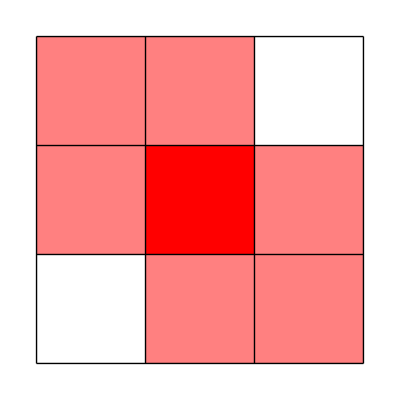

```mathematica
ArrayPlot[{{1,1,0},{1,2,1},{0,1,1}},ColorRules->{2->Red,1->Pink,0->White},Mesh->True,MeshStyle->{Black,Thick}]
```

This is my “square hexagonal lattice.” Cell (i,j) in red, is adjacent to cells (i-1,j-1), (i-1,j), (i,j-1), (i,j+1), (i+1,j),(i+1,j+1) shown in pink.

```mathematica
deltaEnergy[i_,j_,array_]:=
(array⟦i,j⟧array⟦i,Mod[j,m]+1⟧+array⟦i,j⟧array⟦i,Mod[j-2,m]+1⟧ (*neighbors in same row *)+
array⟦i,j⟧array⟦Mod[i-2,n]+1,j⟧+array⟦i,j⟧array⟦Mod[i-2,n]+1,Mod[j-2,m]+1⟧+ (*neighbors in row above*)
array⟦i,j⟧array⟦Mod[i,n]+1,j⟧+array⟦i,j⟧array⟦Mod[i,n]+1,Mod[j,m]+1⟧) (*neighbors in row below*)-((array⟦i,j⟧/.{-1->1,1->-1})array⟦i,Mod[j,m]+1⟧+(array⟦i,j⟧/.{-1->1,1->-1})array⟦i,Mod[j-2,m]+1⟧+(*neighbors in same row *)
(array⟦i,j⟧/.{-1->1,1->-1})array⟦Mod[i-2,n]+1,j⟧+(array⟦i,j⟧/.{-1->1,1->-1})array⟦Mod[i-2,n]+1,Mod[j-2,m]+1⟧+(*neighbors in row above*)
(array⟦i,j⟧/.{-1->1,1->-1})array⟦Mod[i,n]+1,j⟧+(array⟦i,j⟧/.{-1->1,1->-1})array⟦Mod[i,n]+1,Mod[j,m]+1⟧ (*neighbors in row below *))
```

Now let’s test that this generally works as expected with a small grid. This will still output a square plot, but the adjacency rules have certain diagonals included.

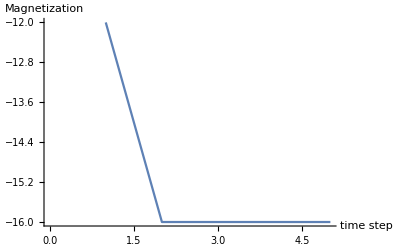

```mathematica
tmax=5; (*Input number of time steps *)
kT=1; (*Input temperature *)
n=4;m=4; (*Input Dimensions *)
fullDataTest={};
magnetizationTest={};
currentArray=RandomInteger[1,{n,m}]/.{0->-1};
fullDataTest=Append[fullDataTest,currentArray];
For[t=1,t⩽tmax,t++,

For[j=1,j≤m,j++,

For[i=1,i≤n,i++,
(*Print[{i,j}];*)
(*Print[currentArray//MatrixForm];*)
If[RandomReal[]<ⅇ^(-deltaEnergy[i,j,currentArray]/kT),(*Print["flip"]; *)currentArray⟦i,j⟧=-currentArray⟦i,j⟧,currentArray⟦i,j⟧=currentArray⟦i,j⟧];
(*Print[currentArray//MatrixForm]*);
]];

(*Outside of our inner two loops, we add the current array to our list of full data and the sum of all of the spins to our list of the magnetiziations*)
fullDataTest=Append[fullDataTest,currentArray];
magnetizationTest=Append[magnetizationTest,Total[Total[currentArray]]];
]
Animate[ArrayPlot[fullDataTest⟦k⟧,ColorRules->{1->Red,-1->Blue}],{k,1,tmax,1}]

ListPlot[magnetizationTest,Joined->True,AxesLabel->{"time step","Magnetization"}]
```

Great! Let’s do this in a bigger grid and a more interesting set of temperatures.

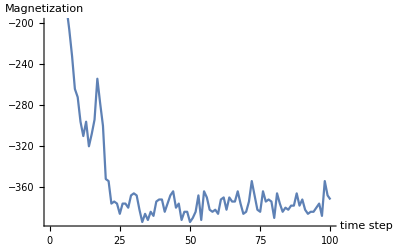

```mathematica
tmax=100; (*Input number of time steps *)
kT=3; (*Input temperature *)
n=20;m=20; (*Input Dimensions *)
fullData={};
magnetization={};
currentArray=RandomInteger[1,{n,m}]/.{0->-1};
fullData=Append[fullData,currentArray];
For[t=1,t⩽tmax,t++,

For[j=1,j≤m,j++,

For[i=1,i≤n,i++,
(*Print[{i,j}];*)
(*Print[currentArray//MatrixForm];*)
If[RandomReal[]<ⅇ^(-deltaEnergy[i,j,currentArray]/kT),(*Print["flip"]; *)currentArray⟦i,j⟧=-currentArray⟦i,j⟧,currentArray⟦i,j⟧=currentArray⟦i,j⟧];
(*Print[currentArray//MatrixForm]*);
]];

(*Outside of our inner two loops, we add the current array to our list of full data and the sum of all of the spins to our list of the magnetiziations*)
fullData=Append[fullData,currentArray];
magnetization=Append[magnetization,Total[Total[currentArray]]];
]
Animate[ArrayPlot[fullData⟦k⟧,ColorRules->{1->Red,-1->Blue}],{k,1,tmax,1}]

ListPlot[magnetization,Joined->True,AxesLabel->{"time step","Magnetization"}]
```

Running this, it looks like the criticle temperature is higher than for the regular flat grid. Neat.

## Anti-ferro magnetic triangular lattice

All we need to do is change the sign of the change in energy. Equivalently, we can swap out e^(-delta energy/kT) for e^(+delta energy/kT).

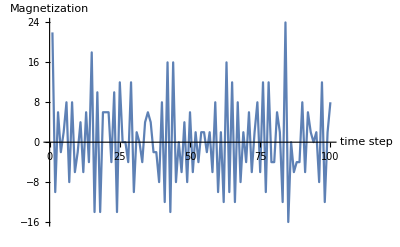

```mathematica
tmax=100; (*Input number of time steps *)
kT=2; (*Input temperature *)
n=20;m=20; (*Input Dimensions *)
fullDataAnti={};
magnetizationAnti={};
currentArray=RandomInteger[1,{n,m}]/.{0->-1};
fullDataAnti=Append[fullDataAnti,currentArray];
For[t=1,t⩽tmax,t++,

For[j=1,j≤m,j++,

For[i=1,i≤n,i++,
(*Print[{i,j}];*)
(*Print[currentArray//MatrixForm];*)
If[RandomReal[]<ⅇ^(deltaEnergy[i,j,currentArray]/kT),(*Print["flip"]; *)currentArray⟦i,j⟧=-currentArray⟦i,j⟧,currentArray⟦i,j⟧=currentArray⟦i,j⟧];
(*Print[currentArray//MatrixForm]*);
]];

(*Outside of our inner two loops, we add the current array to our list of full data and the sum of all of the spins to our list of the magnetiziations*)
fullDataAnti=Append[fullDataAnti,currentArray];
magnetizationAnti=Append[magnetizationAnti,Total[Total[currentArray]]];
]
Animate[ArrayPlot[fullDataAnti⟦k⟧,ColorRules->{1->Red,-1->Blue}],{k,1,tmax,1}]

ListPlot[magnetizationAnti,Joined->True,AxesLabel->{"time step","Magnetization"}]
```

This just oscillates about a magnetism of zero. I think if I watch it for too long, it’ll give me a headache.